# Figure 1, Supplementary Table S1B, Supplementary Table S2B, Supplementary Table S3B

```mathematica
data=Import[NotebookDirectory[]<>"nature25475-f1 - without single day ongoing responses.xlsx","XLSX"]⟦1⟧;
AllMutationTumorTypePairs=Intersection[data⟦2;;,{5,6}⟧];
```

```mathematica
data⟦1;;10⟧//TableForm
```

Subject | Gene | Qualifying Mutation | Allele/Domain | Bubble_Group | Tumor Type | Criteria | Percentage Change of Tumor Measurement | Best Overall Response | Progression-Free Survival Time (Months) | Ongoing
120. | ERBB2 | G778_P780dup | Exon20 Insertion Hotspot | Exon20 Insertion Hotspot | Breast | None | NA | SD | 20.0411 | NO
28. | ERBB2 | L755S | PKD Hotspot | L755 Hotspot | Breast | None | NA | PD | 1.34702 | NO
9. | ERBB2 | G776V  | PKD Hotspot | PKD Hotspot | Breast | None | NA | NONE | 4.3039 | NO
22. | ERBB2 | V777L | PKD Hotspot | V777 Hotspot | Breast | None | NA | PD | 0.952772 | NO
69. | ERBB2 | L755S | PKD Hotspot | L755 Hotspot | Breast | PERCIST | 31.3113 | PD | 1.70842 | NO
64. | ERBB2 | V777L | PKD Hotspot | V777 Hotspot | Breast | RECIST | 26.1053 | PD | 1.87269 | NO
66. | ERBB2 | L755S | PKD Hotspot | L755 Hotspot | Breast | RECIST | 2.54237 | PD | 1.80698 | NO
52. | ERBB2 | V777L | PKD Hotspot | V777 Hotspot | Breast | RECIST | 1.26582 | PD | 1.67556 | NO
71. | ERBB2 | L841V | Other Nonhotspot | PKD Nonhotspot | Breast | RECIST | 0. | SD | 2.75975 | NO

```mathematica
BonferonniCorrectionForAllTumorAndMutationSubtypes=Length[AllMutationTumorTypePairs]
```

50

```mathematica
AllPFSMeasurements=Select[data⟦2;;,{10,11}⟧,#⟦1⟧≠"NA"&]/.{"NO"->0,"YES"->1};
```

```mathematica
RelativeRiskCalculation[descriptors_,eventdata_,PrintTable_(* set to 1 to print out the statistical table of Cox Model output *)]:=Module[{MyModelFit,RelativeRisk,RelativeRiskLowerConfidenceInterval,RelativeRiskUpperConfidenceInterval,PValue},
MyModelFit=CoxModelFit[{descriptors,eventdata},{treatment},{treatment},NominalVariables->treatment];

If[PrintTable==1,Print[MyModelFit["ParameterTable"]]];

RelativeRisk=MyModelFit["RelativeRisk"]⟦1⟧;
RelativeRiskLowerConfidenceInterval=MyModelFit["RelativeRiskConfidenceIntervals"]⟦1,1⟧;
RelativeRiskUpperConfidenceInterval=MyModelFit["RelativeRiskConfidenceIntervals"]⟦1,2⟧;
PValue=MyModelFit["TestTable"]⟦1,1,-1,-1⟧;

{RelativeRiskLowerConfidenceInterval,RelativeRisk,RelativeRiskUpperConfidenceInterval,PValue}
]
```

## analysis of all tumor types PFS

```mathematica
(*Extract PFS data from CSV file, plot all values from largest to smallest*)
AllPFSMeasurements=Select[data⟦2;;,{10,11}⟧,#⟦1⟧≠"NA"&]/.{"NO"->0,"YES"->1};
```

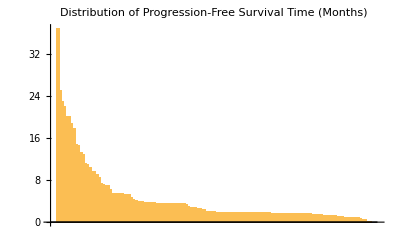

```mathematica
BarChart[Reverse[Sort[AllPFSMeasurements⟦All,1⟧]], PlotLabel->Style["Distribution of Progression-Free Survival Time (Months)",FontSize->12, FontFamily->"Arial"]]
```

```mathematica
PFSAndTumorType=Select[data⟦2;;,{6,10,11}⟧,#⟦2⟧≠"NA"&];
PFSAndMutationTypeAll=Select[data⟦2;;,{5,10,11}⟧,#⟦2⟧≠"NA"&]; 
MutationTypesAll=Sort[Tally[data⟦2;;,5⟧],#1⟦2⟧>#2⟦2⟧&];
MutationTypesAll//TableForm
(* here I map a maximum value onto PFS time *)

ERBB2hotspot={"Exon20 Insertion Hotspot","L755 Hotspot","Other Hotspot","PKD Hotspot","S310 Hotspot","V777 Hotspot"};
ERBB2nonhotspot={"Other Nonhotspot","PKD Nonhotspot"};
ERBB3hotspot={"ERBB3 Hotspot"};
ERBB3nonhotspot={"ERBB3 Nonhotspot"};
ERBB2hotspotResponses=Select[PFSAndMutationTypeAll,MemberQ[ERBB2hotspot,#⟦1⟧]&];
ERBB2nonhotspotResponses=Select[PFSAndMutationTypeAll,MemberQ[ERBB2nonhotspot,#⟦1⟧]&];
ERBB3hotspotResponses=Select[PFSAndMutationTypeAll,MemberQ[ERBB3hotspot,#⟦1⟧]&];
ERBB3nonhotspotResponses=Select[PFSAndMutationTypeAll,MemberQ[ERBB3nonhotspot,#⟦1⟧]&];

TargetAndHotspotStratifiedResponses=Join[
Table[{"ERBB2 Hotspot",i⟦2⟧, i⟦3⟧},{i,ERBB2hotspotResponses}],
Table[{"ERBB2 Nonhotspot",i⟦2⟧, i⟦3⟧},{i,ERBB2nonhotspotResponses}],
Table[{"ERBB3 Hotspot",i⟦2⟧, i⟦3⟧},{i,ERBB3hotspotResponses}],
Table[{"ERBB3 Nonhotspot",i⟦2⟧, i⟦3⟧},{i,ERBB3nonhotspotResponses}]
];

MutationTypes={
{"ERBB2 Hotspot","ERBB2 Nonhotspot","ERBB3 Hotspot","ERBB3 Nonhotspot"}
,
{Length[ERBB2hotspotResponses],Length[ERBB2nonhotspotResponses],Length[ERBB3hotspotResponses],Length[ERBB3nonhotspotResponses]}
}ᵀ;

MutationTypes//TableForm

MeanResponsePerMutationTypeAll=Table[{MutationTypesAll⟦i,1⟧,Mean[Select[PFSAndMutationTypeAll,#⟦1⟧==MutationTypesAll⟦i,1⟧&]⟦All,2⟧]},{i,1,Length[MutationTypesAll]}];
MeanResponsePerMutationTypeAll//TableForm
MedianResponsePerMutationTypeAll=Table[{MutationTypesAll⟦i,1⟧,Median[Select[PFSAndMutationTypeAll,#⟦1⟧==MutationTypesAll⟦i,1⟧&]⟦All,2⟧]},{i,1,Length[MutationTypesAll]}];
MedianResponsePerMutationTypeAll//TableForm
MeanResponsePerMutationType=Table[{MutationTypes⟦i,1⟧,Mean[Select[TargetAndHotspotStratifiedResponses,#⟦1⟧==MutationTypes⟦i,1⟧&]⟦All,2⟧]},{i,1,Length[MutationTypes]}];
MeanResponsePerMutationType//TableForm
MedianResponsePerMutationType=Table[{MutationTypes⟦i,1⟧,Median[Select[TargetAndHotspotStratifiedResponses,#⟦1⟧==MutationTypes⟦i,1⟧&]⟦All,2⟧]},{i,1,Length[MutationTypes]}];
MedianResponsePerMutationType//TableForm



AllTumorsEventTimes=AllPFSMeasurements⟦All,1⟧;
AllTumorsCensoring=AllPFSMeasurements⟦All,2⟧;
PFSAndMutationTypeAll[[1,2]]
```

S310 Hotspot | 30
Exon20 Insertion Hotspot | 26
V777 Hotspot | 15
PKD Hotspot | 14
L755 Hotspot | 13
ERBB3 Hotspot | 12
PKD Nonhotspot | 11
Other Hotspot | 8
ERBB3 Nonhotspot | 4
Other Nonhotspot | 4

ERBB2 Hotspot | 106
ERBB2 Nonhotspot | 15
ERBB3 Hotspot | 12
ERBB3 Nonhotspot | 4

S310 Hotspot | 5.91047
Exon20 Insertion Hotspot | 6.91076
V777 Hotspot | 2.67433
PKD Hotspot | 3.36756
L755 Hotspot | 4.76386
ERBB3 Hotspot | 2.2423
PKD Nonhotspot | 2.77469
Other Hotspot | 4.02875
ERBB3 Nonhotspot | 1.60986
Other Nonhotspot | 1.2731

S310 Hotspot | 2.26694
Exon20 Insertion Hotspot | 4.02464
V777 Hotspot | 1.70842
PKD Hotspot | 3.49897
L755 Hotspot | 3.58111
ERBB3 Hotspot | 1.79055
PKD Nonhotspot | 1.87269
Other Hotspot | 2.71047
ERBB3 Nonhotspot | 1.54415
Other Nonhotspot | 1.56057

ERBB2 Hotspot | 5.07938
ERBB2 Nonhotspot | 2.37426
ERBB3 Hotspot | 2.2423
ERBB3 Nonhotspot | 1.60986

ERBB2 Hotspot | 2.89117
ERBB2 Nonhotspot | 1.83984
ERBB3 Hotspot | 1.79055
ERBB3 Nonhotspot | 1.54415

20.0411

```mathematica
TumorTypes=Sort[Tally[data⟦2;;,6⟧],#1⟦2⟧>#2⟦2⟧&];
TumorTypes//TableForm
```

Breast | 25
Lung | 23
HER3_NOS | 16
Bladder | 16
Other | 15
Colorectal | 12
Biliary tract | 9
Endometrial | 7
Gastroesophageal | 5
Cervical | 5
Ovarian | 4

```mathematica
SetOfResponsesPerTumorType=Table[Select[PFSAndTumorType,#⟦1⟧==TumorTypes⟦i,1⟧&]/.{"NO"->0,"YES"->1},{i,1,Length[TumorTypes]}];
SetOfResponsesPerMutationType=Table[Select[TargetAndHotspotStratifiedResponses,#⟦1⟧==MutationTypes⟦i,1⟧&]/.{"NO"->0,"YES"->1},{i,1,Length[MutationTypes]}];
SetOfResponsesPerMutationTypeAll=Table[Select[PFSAndMutationTypeAll,#⟦1⟧==MutationTypesAll⟦i,1⟧&]/.{"NO"->0,"YES"->1},{i,1,Length[MutationTypesAll]}];
```

```mathematica
HazardRatioVersusAllTumorTypes[Eventtimes_,Censoring_]:=Module[{TreatmentLabels,SubgroupAndAllEventTimes,SubgroupAndAllCensoring,SubgroupAndAllEventData,lowerHR,HR,upperHR,Pvalue},

TreatmentLabels=Join[Table["Subgroup",{Length[Eventtimes]}],Table["All",{Length[AllTumorsEventTimes]}]];
SubgroupAndAllEventTimes=Join[Eventtimes,AllTumorsEventTimes];
SubgroupAndAllCensoring=Join[Censoring,AllTumorsCensoring];
SubgroupAndAllEventData=EventData[SubgroupAndAllEventTimes,SubgroupAndAllCensoring];

{lowerHR,HR,upperHR,Pvalue}=RelativeRiskCalculation[TreatmentLabels,SubgroupAndAllEventData,0];

{lowerHR,HR,upperHR,Pvalue}
]
```

```mathematica
HazardRatioVersusAllTumorTypes[SetOfResponsesPerTumorType⟦2,All,2⟧,SetOfResponsesPerTumorType⟦2,All,3⟧]
HazardRatioVersusAllTumorTypes[SetOfResponsesPerMutationType⟦2,All,2⟧,SetOfResponsesPerMutationType⟦2,All,3⟧]
HazardRatioVersusAllTumorTypes[SetOfResponsesPerMutationTypeAll⟦2,All,2⟧,SetOfResponsesPerMutationTypeAll⟦2,All,3⟧]
```

{0.365984,0.58923,0.948653,0.0276965}

{0.8983,1.57528,2.76246,0.109769}

{0.42655,0.667374,1.04416,0.0746548}

```mathematica
HRperTumorType=Table[Flatten[{TumorTypes⟦i,1⟧,HazardRatioVersusAllTumorTypes[SetOfResponsesPerTumorType⟦i,All,2⟧,SetOfResponsesPerTumorType⟦i,All,3⟧]}],{i,1,Length[TumorTypes]}];
Prepend[HRperTumorType,{"TUMOR TYPE","LOWER HR","HR","UPPER HR","P VALUE"}]//TableForm

HRperMutationType=Table[Flatten[{MutationTypes⟦i,1⟧,HazardRatioVersusAllTumorTypes[SetOfResponsesPerMutationType⟦i,All,2⟧,SetOfResponsesPerMutationType⟦i,All,3⟧]}],{i,1,Length[MutationTypes]}];
Prepend[HRperMutationType,{"MUTATION TYPE","LOWER HR","HR","UPPER HR","P VALUE"}]//TableForm

HRperMutationTypeAll=Table[Flatten[{MutationTypesAll⟦i,1⟧,HazardRatioVersusAllTumorTypes[SetOfResponsesPerMutationTypeAll⟦i,All,2⟧,SetOfResponsesPerMutationTypeAll⟦i,All,3⟧]}],{i,1,Length[MutationTypesAll]}];
Prepend[HRperMutationTypeAll,{"MUTATION TYPE ALL","LOWER HR","HR","UPPER HR","P VALUE"}]//TableForm
```

TUMOR TYPE | LOWER HR | HR | UPPER HR | P VALUE
Breast | 0.605141 | 0.938648 | 1.45596 | 0.777381
Lung | 0.365984 | 0.58923 | 0.948653 | 0.0276965
HER3_NOS | 1.19075 | 2.02876 | 3.45653 | 0.00790338
Bladder | 0.574493 | 0.987428 | 1.69717 | 0.963483
Other | 0.7302 | 1.36529 | 2.55275 | 0.32753
Colorectal | 0.892544 | 1.62358 | 2.95337 | 0.108921
Biliary tract | 0.509401 | 1.094 | 2.34949 | 0.817751
Endometrial | 0.457843 | 0.983548 | 2.11288 | 0.966084
Gastroesophageal | 0.842539 | 2.07425 | 5.10659 | 0.104666
Cervical | 0.132983 | 0.423973 | 1.3517 | 0.135292
Ovarian | 0.21165 | 0.863317 | 3.52146 | 0.837504

MUTATION TYPE | LOWER HR | HR | UPPER HR | P VALUE
ERBB2 Hotspot | 0.665486 | 0.872572 | 1.1441 | 0.323707
ERBB2 Nonhotspot | 0.8983 | 1.57528 | 2.76246 | 0.109769
ERBB3 Hotspot | 0.996437 | 1.81928 | 3.32161 | 0.0479942
ERBB3 Nonhotspot | 1.1086 | 3.04783 | 8.3793 | 0.0230226

MUTATION TYPE ALL | LOWER HR | HR | UPPER HR | P VALUE
S310 Hotspot | 0.518088 | 0.805437 | 1.25216 | 0.335597
Exon20 Insertion Hotspot | 0.42655 | 0.667374 | 1.04416 | 0.0746548
V777 Hotspot | 0.886067 | 1.54801 | 2.70447 | 0.121802
PKD Hotspot | 0.555449 | 1.00892 | 1.83259 | 0.976745
L755 Hotspot | 0.552723 | 0.981033 | 1.74124 | 0.947843
ERBB3 Hotspot | 0.996437 | 1.81928 | 3.32161 | 0.0479942
PKD Nonhotspot | 0.66032 | 1.26628 | 2.42833 | 0.476282
Other Hotspot | 0.362768 | 0.824922 | 1.87584 | 0.645597
ERBB3 Nonhotspot | 1.1086 | 3.04783 | 8.3793 | 0.0230226
Other Nonhotspot | 1.43424 | 3.97618 | 11.0233 | 0.0041238

```mathematica
MeanResponsePerTumorType=Table[{TumorTypes⟦i,1⟧,HRperTumorType⟦i,3⟧},{i,1,Length[TumorTypes]}];
MeanResponsePerTumorType//TableForm
MeanResponsePerMutationType//TableForm
MeanResponsePerMutationTypeAll//TableForm
```

Breast | 0.938648
Lung | 0.58923
HER3_NOS | 2.02876
Bladder | 0.987428
Other | 1.36529
Colorectal | 1.62358
Biliary tract | 1.094
Endometrial | 0.983548
Gastroesophageal | 2.07425
Cervical | 0.423973
Ovarian | 0.863317

ERBB2 Hotspot | 5.07938
ERBB2 Nonhotspot | 2.37426
ERBB3 Hotspot | 2.2423
ERBB3 Nonhotspot | 1.60986

S310 Hotspot | 5.91047
Exon20 Insertion Hotspot | 6.91076
V777 Hotspot | 2.67433
PKD Hotspot | 3.36756
L755 Hotspot | 4.76386
ERBB3 Hotspot | 2.2423
PKD Nonhotspot | 2.77469
Other Hotspot | 4.02875
ERBB3 Nonhotspot | 1.60986
Other Nonhotspot | 1.2731

```mathematica
CalculateHRFromSubSample[samplesize_]:=Module[{SubSample,SubSampleEventTimes,SubSampleCensoring,TreatmentLabels,SubgroupAndAllEventTimes,SubgroupAndAllCensoring,SubgroupAndAllEventData,lowerHR,HR,upperHR,Pvalue},

SubSample=RandomSample[AllPFSMeasurements,samplesize];
SubSampleEventTimes=SubSample⟦All,1⟧;
SubSampleCensoring=SubSample⟦All,2⟧;

TreatmentLabels=Join[Table["Subgroup",{samplesize}],Table["All",{Length[AllTumorsEventTimes]}]];
SubgroupAndAllEventTimes=Join[SubSampleEventTimes,AllTumorsEventTimes];
SubgroupAndAllCensoring=Join[SubSampleCensoring,AllTumorsCensoring];
SubgroupAndAllEventData=EventData[SubgroupAndAllEventTimes,SubgroupAndAllCensoring];

{lowerHR,HR,upperHR,Pvalue}=RelativeRiskCalculation[TreatmentLabels,SubgroupAndAllEventData,0];

HR
]
```

### importing and plotting

```mathematica
SetDirectory[NotebookDirectory[]]; 
ManySamplesOfTrialMatchedSizeMutation=Table[{MutationTypes⟦i,1⟧,Import[NotebookDirectory[]<>StringJoin[MutationTypes⟦i,1⟧,"NullHRs.csv"]]⟦All,1⟧},{i,1,Length[MutationTypes]}];
```

```mathematica
ManySamplesOfTrialMatchedSizeMutationAll=Table[{MutationTypesAll⟦i,1⟧,Import[NotebookDirectory[]<>StringJoin[MutationTypesAll⟦i,1⟧,"NullHRs.csv"]]⟦All,1⟧},{i,1,Length[MutationTypesAll]}];
```

### Probability of larger benefit (one-sided)

```mathematica
NumberOfRepeats=10^6; 
PValuesByMutationType=Table[{MutationTypes⟦i,1⟧,Length[Select[ManySamplesOfTrialMatchedSizeMutation⟦i,2⟧,#<HRperMutationType⟦i,3⟧&]]/NumberOfRepeats//N},{i,1,4}]
PValuesByMutationTypeAll=Table[{MutationTypesAll⟦i,1⟧,Length[Select[ManySamplesOfTrialMatchedSizeMutationAll⟦i,2⟧,#<HRperMutationTypeAll⟦i,3⟧&]]/NumberOfRepeats//N},{i,1,10}]
```

{{ERBB2 Hotspot,0.000528},{ERBB2 Nonhotspot,0.950415},{ERBB3 Hotspot,0.970208},{ERBB3 Nonhotspot,0.961921}}

{{S310 Hotspot,0.093662},{Exon20 Insertion Hotspot,0.011024},{V777 Hotspot,0.943859},{PKD Hotspot,0.49856},{L755 Hotspot,0.455984},{ERBB3 Hotspot,0.970208},{PKD Nonhotspot,0.759249},{Other Hotspot,0.273706},{ERBB3 Nonhotspot,0.961921},{Other Nonhotspot,0.984698}}

```mathematica
SortedPValuesM=Join[{Range[4]},Sort[PValuesByMutationType,#1⟦2⟧<#2⟦2⟧&]ᵀ]ᵀ;
SortedPValuesM//TableForm
SortedPValuesMA=Join[{Range[10]},Sort[PValuesByMutationTypeAll,#1⟦2⟧<#2⟦2⟧&]ᵀ]ᵀ;
SortedPValuesMA//TableForm
```

1 | ERBB2 Hotspot | 0.000528
2 | ERBB2 Nonhotspot | 0.950415
3 | ERBB3 Nonhotspot | 0.961921
4 | ERBB3 Hotspot | 0.970208

1 | Exon20 Insertion Hotspot | 0.011024
2 | S310 Hotspot | 0.093662
3 | Other Hotspot | 0.273706
4 | L755 Hotspot | 0.455984
5 | PKD Hotspot | 0.49856
6 | PKD Nonhotspot | 0.759249
7 | V777 Hotspot | 0.943859
8 | ERBB3 Nonhotspot | 0.961921
9 | ERBB3 Hotspot | 0.970208
10 | Other Nonhotspot | 0.984698

```mathematica
Table[{SortedPValuesM⟦i,1⟧,SortedPValuesM⟦i,2⟧,SortedPValuesM⟦i,3⟧,(* benjamini-hochberg critical value: (i/m)*Q *)(SortedPValuesM⟦i,1⟧/Length[SortedPValuesM]*(* Q = 0.25 *)0.25//N)},{i,1,Length[SortedPValuesM]}]//TableForm
Table[{SortedPValuesMA⟦i,1⟧,SortedPValuesMA⟦i,2⟧,SortedPValuesMA⟦i,3⟧,(* benjamini-hochberg critical value: (i/m)*Q *)(SortedPValuesMA⟦i,1⟧/Length[SortedPValuesMA]*(* Q = 0.25 *)0.25//N)},{i,1,Length[SortedPValuesMA]}]//TableForm
```

1 | ERBB2 Hotspot | 0.000528 | 0.0625
2 | ERBB2 Nonhotspot | 0.950415 | 0.125
3 | ERBB3 Nonhotspot | 0.961921 | 0.1875
4 | ERBB3 Hotspot | 0.970208 | 0.25

1 | Exon20 Insertion Hotspot | 0.011024 | 0.025
2 | S310 Hotspot | 0.093662 | 0.05
3 | Other Hotspot | 0.273706 | 0.075
4 | L755 Hotspot | 0.455984 | 0.1
5 | PKD Hotspot | 0.49856 | 0.125
6 | PKD Nonhotspot | 0.759249 | 0.15
7 | V777 Hotspot | 0.943859 | 0.175
8 | ERBB3 Nonhotspot | 0.961921 | 0.2
9 | ERBB3 Hotspot | 0.970208 | 0.225
10 | Other Nonhotspot | 0.984698 | 0.25

### CONTINUING

```mathematica
HRlogframeticks=Join[
Table[{x,10^x,{0,0.05}},{x,{Log[10,0.3],Log[10,0.5],Log[10,1],Log[10,2],Log[10,4]}}],
Flatten[
Table[
Table[{Log[10,x],"",{0,0.02}},{x,1*10^y,9*10^y,1*10^y}],
{y,-5,5,1}]
,1]
];
```

```mathematica
HistogramOfMeanResponseWithinATumorTypeMutation[i_]:=Module[{},

HistTumor=Histogram[Log[10,ManySamplesOfTrialMatchedSizeMutation⟦i,2⟧],{Log[10,1/4],Log[10,4],bs},"Probability",(*PlotLabel->Style[ManySamplesOfTrialMatchedSize⟦i,1⟧,Black,FontSize->11,FontFamily->"Arial"],*)PlotRange->{{Log[10,0.25],Log[10,4]},{0,ph}},PlotRangePadding->None,Frame->{{False,False},{True,False}},FrameStyle->Directive[Black,Thickness[Medium]],Epilog->{Red,AbsoluteThickness[2],Line[{{Log[10,HRperMutationType⟦i,3⟧],0},{Log[10,HRperMutationType⟦i,3⟧],ph}}]},ChartStyle->Directive[EdgeForm[None],Lighter[ColorData[3,6],0.5]],FrameTicks->{{None,None},{HRlogframeticks,None}},BaseStyle->{FontFamily->"Arial",FontSize->10},AspectRatio->0.3,ImagePadding->{{20,20},{40,5}},FrameLabel->{None,None(*"Average duration of PFS (months)","Probability (%)"*)},LabelStyle->Opacity[1],ImageSize->{{180},{300}}
];

 Export[NotebookDirectory[]<>ManySamplesOfTrialMatchedSizeMutation⟦i,1⟧<>"_Mutation_Histogram.pdf", HistTumor,"PDF"];

HistTumor
]; 

HistogramOfMeanResponseWithinATumorTypeMutationAll[i_]:=Module[{},

HistTumor=Histogram[Log[10,ManySamplesOfTrialMatchedSizeMutationAll⟦i,2⟧],{Log[10,1/4],Log[10,4],bs},"Probability",(*PlotLabel->Style[ManySamplesOfTrialMatchedSize⟦i,1⟧,Black,FontSize->11,FontFamily->"Arial"],*)PlotRange->{{Log[10,0.25],Log[10,4]},{0,ph}},PlotRangePadding->None,Frame->{{False,False},{True,False}},FrameStyle->Directive[Black,Thickness[Medium]],Epilog->{Red,AbsoluteThickness[2],Line[{{Log[10,HRperMutationTypeAll⟦i,3⟧],0},{Log[10,HRperMutationTypeAll⟦i,3⟧],ph}}]},ChartStyle->Directive[EdgeForm[None],Lighter[ColorData[3,6],0.5]],FrameTicks->{{None,None},{HRlogframeticks,None}},BaseStyle->{FontFamily->"Arial",FontSize->10},AspectRatio->0.3,ImagePadding->{{20,20},{40,5}},FrameLabel->{None,None(*"Average duration of PFS (months)","Probability (%)"*)},LabelStyle->Opacity[1],ImageSize->{{180},{300}}
];

 Export[NotebookDirectory[]<>ManySamplesOfTrialMatchedSizeMutationAll⟦i,1⟧<>"_MutationAll_Histogram.pdf", HistTumor,"PDF"];

HistTumor
]; 


HistogramOfMeanResponseWithinATumorType[i_]:=Module[{},

HistTumor=Histogram[Log[10,ManySamplesOfTrialMatchedSize⟦i,2⟧],{Log[10,1/4],Log[10,4],0.025},"Probability",(*PlotLabel->Style[ManySamplesOfTrialMatchedSize⟦i,1⟧,Black,FontSize->11,FontFamily->"Arial"],*)PlotRange->{{Log[10,0.25],Log[10,4]},{0,ph}},PlotRangePadding->None,Frame->{{False,False},{True,False}},FrameStyle->Directive[Black,Thickness[Medium]],Epilog->{Red,AbsoluteThickness[2],Line[{{Log[10,HRperTumorType⟦i,3⟧],0},{Log[10,HRperTumorType⟦i,3⟧],ph}}]},ChartStyle->Directive[EdgeForm[None],Lighter[ColorData[3,6],0.5]],FrameTicks->{{None,None},{HRlogframeticks,None}},BaseStyle->{FontFamily->"Arial",FontSize->10},AspectRatio->0.3,ImagePadding->{{20,20},{40,5}},FrameLabel->{None,None(*"Average duration of PFS (months)","Probability (%)"*)},LabelStyle->Opacity[1],ImageSize->{{180},{300}}
];

 Export[NotebookDirectory[]<>ManySamplesOfTrialMatchedSize⟦i,1⟧<>"_Histogram.pdf", HistTumor,"PDF"];

HistTumor
];
```

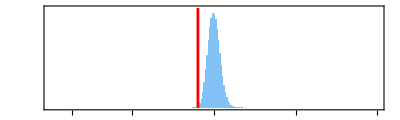

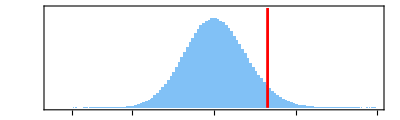

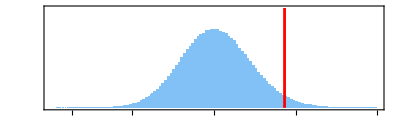

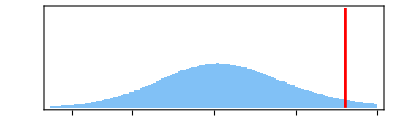

```mathematica
For [i=1, i≤ 1, i++, 
ph (* plot height *)=0.1;
bs=0.005;
HistogramOfMeanResponseWithinATumorTypeMutation[i];
Print[HistTumor]]; 
For [i=2, i≤ 4, i++, 
ph (* plot height *)=0.04;
bs=0.01;
HistogramOfMeanResponseWithinATumorTypeMutation[i];
Print[HistTumor]];
```

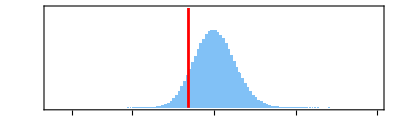

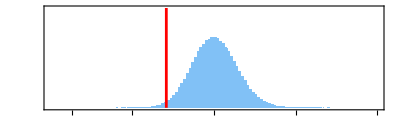

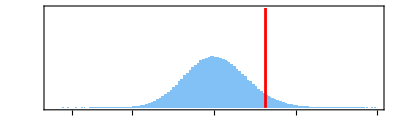

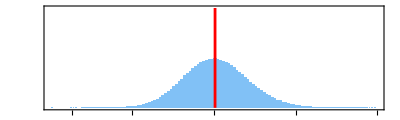

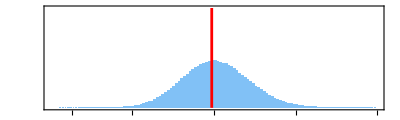

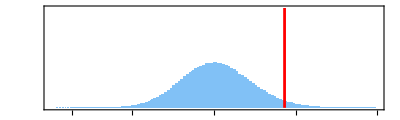

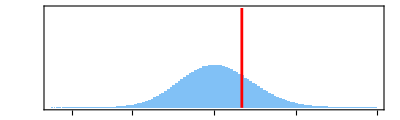

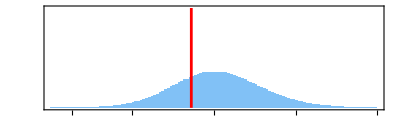

```mathematica
For [i=1, i≤ 10, i++, 
bs=0.01;
ph=0.07;
HistogramOfMeanResponseWithinATumorTypeMutationAll[i];
Print[HistTumor]];
```

## analysis of all tumor types PFS by histology

```mathematica
TumorTypes=Sort[Tally[data⟦2;;,6⟧],#1⟦2⟧>#2⟦2⟧&];
```

```mathematica
TumorTypes=Sort[Tally[data⟦2;;,6⟧],#1⟦2⟧>#2⟦2⟧&];
TumorTypes//TableForm
```

Breast | 25
Lung | 23
HER3_NOS | 16
Bladder | 16
Other | 15
Colorectal | 12
Biliary tract | 9
Endometrial | 7
Gastroesophageal | 5
Cervical | 5
Ovarian | 4

```mathematica
OfInterest= {1,2,4,6,7,8,9,10,11}
OfInterest[[1]]
ManySamplesOfTrialMatchedSize=Table[{TumorTypes⟦OfInterest[[i]],1⟧,Import[StringJoin[TumorTypes⟦OfInterest[[i]],1⟧,"NullHRs.csv"]]},{i,1,Length[OfInterest]}];
```

{1,2,4,6,7,8,9,10,11}

1

```mathematica
SetOfResponsesPerTumorType=Table[Select[PFSAndTumorType,#⟦1⟧==TumorTypes⟦i,1⟧&]/.{"NO"->0,"YES"->1},{i,1,Length[TumorTypes]}];
```

```mathematica
SetOfResponsesPerTumorType⟦1⟧
```

{{Breast,20.0411,0},{Breast,1.34702,0},{Breast,4.3039,0},{Breast,0.952772,0},{Breast,1.70842,0},{Breast,1.87269,0},{Breast,1.80698,0},{Breast,1.67556,0},{Breast,2.75975,0},{Breast,3.8768,0},{Breast,3.71253,0},{Breast,3.48255,0},{Breast,7.19507,0},{Breast,3.61396,0},{Breast,3.48255,0},{Breast,1.21561,0},{Breast,1.9384,0},{Breast,9.03491,0},{Breast,3.54825,0},{Breast,5.38809,0},{Breast,3.61396,0},{Breast,5.51951,0},{Breast,7.32649,0},{Breast,14.6201,1},{Breast,1.64271,0}}

```mathematica
HazardRatioVersusAllTumorTypes[Eventtimes_,Censoring_]:=Module[{TreatmentLabels,SubgroupAndAllEventTimes,SubgroupAndAllCensoring,SubgroupAndAllEventData,lowerHR,HR,upperHR,Pvalue},

TreatmentLabels=Join[Table["Subgroup",{Length[Eventtimes]}],Table["All",{Length[AllTumorsEventTimes]}]];
SubgroupAndAllEventTimes=Join[Eventtimes,AllTumorsEventTimes];
SubgroupAndAllCensoring=Join[Censoring,AllTumorsCensoring];
SubgroupAndAllEventData=EventData[SubgroupAndAllEventTimes,SubgroupAndAllCensoring];

{lowerHR,HR,upperHR,Pvalue}=RelativeRiskCalculation[TreatmentLabels,SubgroupAndAllEventData,0];

{lowerHR,HR,upperHR,Pvalue}
]
```

```mathematica
(* event times in breast tumors *)SetOfResponsesPerTumorType⟦1,All,2⟧
%//Length
(* censoring in breast tumors *)SetOfResponsesPerTumorType⟦1,All,3⟧
%//Length
```

{20.0411,1.34702,4.3039,0.952772,1.70842,1.87269,1.80698,1.67556,2.75975,3.8768,3.71253,3.48255,7.19507,3.61396,3.48255,1.21561,1.9384,9.03491,3.54825,5.38809,3.61396,5.51951,7.32649,14.6201,1.64271}

25

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0}

25

```mathematica
HazardRatioVersusAllTumorTypes[SetOfResponsesPerTumorType⟦2,All,2⟧,SetOfResponsesPerTumorType⟦2,All,3⟧]
```

{0.365984,0.58923,0.948653,0.0276965}

```mathematica
HRperTumorType=Table[Flatten[{TumorTypes⟦i,1⟧,HazardRatioVersusAllTumorTypes[SetOfResponsesPerTumorType⟦i,All,2⟧,SetOfResponsesPerTumorType⟦i,All,3⟧]}],{i,1,Length[TumorTypes]}];
Prepend[HRperTumorType,{"TUMOR TYPE","LOWER HR","HR","UPPER HR","P VALUE"}]//TableForm
```

TUMOR TYPE | LOWER HR | HR | UPPER HR | P VALUE
Breast | 0.605141 | 0.938648 | 1.45596 | 0.777381
Lung | 0.365984 | 0.58923 | 0.948653 | 0.0276965
HER3_NOS | 1.19075 | 2.02876 | 3.45653 | 0.00790338
Bladder | 0.574493 | 0.987428 | 1.69717 | 0.963483
Other | 0.7302 | 1.36529 | 2.55275 | 0.32753
Colorectal | 0.892544 | 1.62358 | 2.95337 | 0.108921
Biliary tract | 0.509401 | 1.094 | 2.34949 | 0.817751
Endometrial | 0.457843 | 0.983548 | 2.11288 | 0.966084
Gastroesophageal | 0.842539 | 2.07425 | 5.10659 | 0.104666
Cervical | 0.132983 | 0.423973 | 1.3517 | 0.135292
Ovarian | 0.21165 | 0.863317 | 3.52146 | 0.837504

```mathematica
MeanResponsePerTumorType=Table[{TumorTypes⟦i,1⟧,HRperTumorType⟦i,3⟧},{i,1,Length[TumorTypes]}];
MeanResponsePerTumorType//TableForm
```

Breast | 0.938648
Lung | 0.58923
HER3_NOS | 2.02876
Bladder | 0.987428
Other | 1.36529
Colorectal | 1.62358
Biliary tract | 1.094
Endometrial | 0.983548
Gastroesophageal | 2.07425
Cervical | 0.423973
Ovarian | 0.863317

```mathematica
CalculateHRFromSubSample[samplesize_]:=Module[{SubSample,SubSampleEventTimes,SubSampleCensoring,TreatmentLabels,SubgroupAndAllEventTimes,SubgroupAndAllCensoring,SubgroupAndAllEventData,lowerHR,HR,upperHR,Pvalue},

SubSample=RandomSample[AllPFSMeasurements,samplesize];
SubSampleEventTimes=SubSample⟦All,1⟧;
SubSampleCensoring=SubSample⟦All,2⟧;

TreatmentLabels=Join[Table["Subgroup",{samplesize}],Table["All",{Length[AllTumorsEventTimes]}]];
SubgroupAndAllEventTimes=Join[SubSampleEventTimes,AllTumorsEventTimes];
SubgroupAndAllCensoring=Join[SubSampleCensoring,AllTumorsCensoring];
SubgroupAndAllEventData=EventData[SubgroupAndAllEventTimes,SubgroupAndAllCensoring];

{lowerHR,HR,upperHR,Pvalue}=RelativeRiskCalculation[TreatmentLabels,SubgroupAndAllEventData,0];

HR
]
```

```mathematica
CalculateHRFromSubSample[10]
```

1.19981

```mathematica
TumorTypes⟦1,1⟧
TumorTypes⟦1,2⟧
```

Breast

25

### Probability of larger benefit (one-sided)

```mathematica
NumberOfRepeats=10^6;
PValuesByTumorType=Table[{TumorTypes⟦OfInterest[[i]],1⟧,Length[Select[Flatten[ManySamplesOfTrialMatchedSize⟦i,2⟧,1],#<HRperTumorType⟦OfInterest[[i]],3⟧&]]/NumberOfRepeats//N},{i,1,9}](* wihout removing breast, not an outlier in this case *)
```

{{Breast,0.362993},{Lung,0.002707},{Bladder,0.466824},{Colorectal,0.937505},{Biliary tract,0.578908},{Endometrial,0.453853},{Gastroesophageal,0.91157},{Cervical,0.027257},{Ovarian,0.346564}}

```mathematica
SortedPValues=Join[{Range[9]},Sort[PValuesByTumorType,#1⟦2⟧<#2⟦2⟧&]ᵀ]ᵀ;
SortedPValues//TableForm
```

1 | Lung | 0.002707
2 | Cervical | 0.027257
3 | Ovarian | 0.346564
4 | Breast | 0.362993
5 | Endometrial | 0.453853
6 | Bladder | 0.466824
7 | Biliary tract | 0.578908
8 | Gastroesophageal | 0.91157
9 | Colorectal | 0.937505

```mathematica
Table[{SortedPValues⟦i,1⟧,SortedPValues⟦i,2⟧,SortedPValues⟦i,3⟧,(* benjamini-hochberg critical value: (i/m)*Q *)(SortedPValues⟦i,1⟧/Length[SortedPValues]*(* Q = 0.25 *)0.25//N)},{i,1,Length[SortedPValues]}]//TableForm
```

1 | Lung | 0.002707 | 0.0277778
2 | Cervical | 0.027257 | 0.0555556
3 | Ovarian | 0.346564 | 0.0833333
4 | Breast | 0.362993 | 0.111111
5 | Endometrial | 0.453853 | 0.138889
6 | Bladder | 0.466824 | 0.166667
7 | Biliary tract | 0.578908 | 0.194444
8 | Gastroesophageal | 0.91157 | 0.222222
9 | Colorectal | 0.937505 | 0.25

### comparison to standard Cox Model P values (no resampling)

```mathematica
Prepend[HRperTumorType⟦{1,2,4,6,7,8,9,10,11}⟧,{"TUMOR TYPE","LOWER HR","HR","UPPER HR","P VALUE"}]//TableForm
```

TUMOR TYPE | LOWER HR | HR | UPPER HR | P VALUE
Breast | 0.605141 | 0.938648 | 1.45596 | 0.777381
Lung | 0.365984 | 0.58923 | 0.948653 | 0.0276965
Bladder | 0.574493 | 0.987428 | 1.69717 | 0.963483
Colorectal | 0.892544 | 1.62358 | 2.95337 | 0.108921
Biliary tract | 0.509401 | 1.094 | 2.34949 | 0.817751
Endometrial | 0.457843 | 0.983548 | 2.11288 | 0.966084
Gastroesophageal | 0.842539 | 2.07425 | 5.10659 | 0.104666
Cervical | 0.132983 | 0.423973 | 1.3517 | 0.135292
Ovarian | 0.21165 | 0.863317 | 3.52146 | 0.837504

```mathematica
HRlogframeticks=Join[
Table[{x,10^x,{0,0.05}},{x,{Log[10,0.3],Log[10,0.5],Log[10,1],Log[10,2],Log[10,4]}}],
Flatten[
Table[
Table[{Log[10,x],"",{0,0.02}},{x,1*10^y,9*10^y,1*10^y}],
{y,-5,5,1}]
,1]
];
```

```mathematica
ph (* plot height *)=0.13;

HistogramOfMeanResponseWithinATumorType[i_]:=Module[{},

HistTumor=Histogram[Log[10,Flatten[ManySamplesOfTrialMatchedSize⟦i,2⟧,1]],{Log[10,1/4],Log[10,4],bs},"Probability",(*PlotLabel->Style[ManySamplesOfTrialMatchedSize⟦i,1⟧,Black,FontSize->11,FontFamily->"Arial"],*)PlotRange->{{Log[10,0.25],Log[10,4]},{0,ph}},PlotRangePadding->None,Frame->{{False,False},{True,False}},FrameStyle->Directive[Black,Thickness[Medium]],Epilog->{Red,AbsoluteThickness[2],Line[{{Log[10,HRperTumorType⟦OfInterest[[i]],3⟧],0},{Log[10,HRperTumorType⟦OfInterest[[i]],3⟧],ph}}]},ChartStyle->Directive[EdgeForm[None],Lighter[ColorData[3,6],0.5]],FrameTicks->{{None,None},{HRlogframeticks,None}},BaseStyle->{FontFamily->"Arial",FontSize->10},AspectRatio->0.3,ImagePadding->{{20,20},{40,5}},FrameLabel->{None,None(*"Average duration of PFS (months)","Probability (%)"*)},LabelStyle->Opacity[1],ImageSize->{{180},{300}}
];

 Export[NotebookDirectory[]<>ManySamplesOfTrialMatchedSize⟦i,1⟧<>"_Histogram.pdf", HistTumor,"PDF"];

HistTumor
];
```

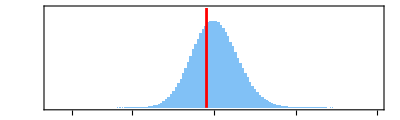

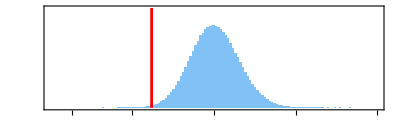

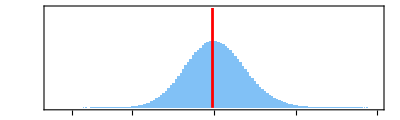

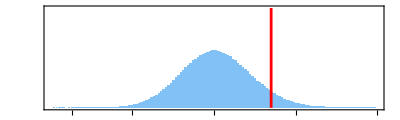

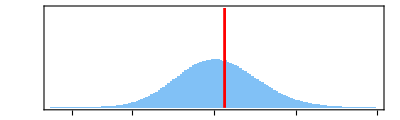

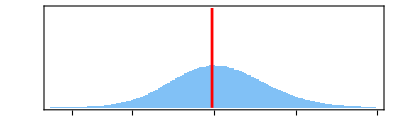

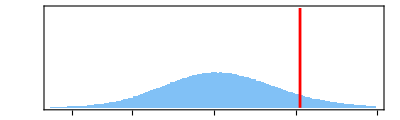

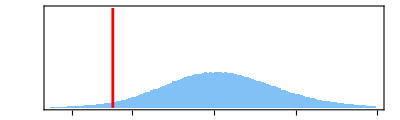

```mathematica
For [i=1, i≤ 9, i++, 
bs=0.009;
ph=0.05;
HistogramOfMeanResponseWithinATumorType[i];
Print[HistTumor]];
```